```mathematica
(* Euclidean METRIC.  E only Test case of CDR-LC which produces moms of asymptotic-QCD DA 6x(1-x) via a continuous weight rho(zz) for the coeff of krel.P in BS ampl *)
```

```mathematica
(* For simple analytic result need constituent q mass Mc = range param of E ampl *)
```

```mathematica
(*  Also test the accuracy of using only 2 discrete zz values *)
```

```mathematica
(* Eonly integral is convergent --NO REGULATOR FACTOR needed. 3 DENOMS  ch limit P^2=0= m_pi^2 *)
```

```mathematica
(* ALGEBRAIC VARIABLES: M fpi *)
```

```mathematica
(* Standard 3 denom Feyn Int: 1/(A B C) = 2! \int JJac/(a1 A +a2 B + a3 C)^3, with a1=x1 a2=(1-x1)x2 a3=1-a1-a2 = (1-x1-(1-x1)x2) and JJac=1-x1 *)
```

```mathematica
JJac=1-x1;  (* cannot simply integrate since a1 a2 not independent, jjac is jacobian *)
```

```mathematica
(0.1 0.2 0.3 ) 2!*NIntegrate[ JJac  /(x1 0.1 +(1-x1)x2 0.2+(1-x1- (1-x1)x2) 0.3)^3, {x1,0,1},{x2,0,1}]
```

1.

```mathematica
pimass= 0.0; Mc=0.4;fpiphys = 0.0924;Nc=3;mmax=10;P2=0.; (* mc = const. mass, p2 is square of 4-vector *)
```

```mathematica
(* Read Package Tracer.m into memnory so can do Dirac traces.   Use, in a separate Matha.nb, in MacBook: << /Users/Tandy/Dropbox/Peter/..../Tracer.m  in updated Matha8; in MacBook Pro: /Users/tandy/petertandy/Dingo-cygwin/Peter/Mathematica/Triangle_Diag_pionFF/Tracer.m 
in MacBookAir: /Users/petertandy/Dropbox/Peter/Mathematica/Triangle_Diag_pionFF/Tracer.m *)
```

```mathematica
<< Documents/mathprograms/Tracer.m
```

Remove::rmnsm: There are no symbols matching ""Tracer`Private`*"".

T R A C E R

=============

A MATHEMATICA PACKAGE FOR GAMMA-ALGEBRA IN ARBITRARY DIMENSIONS

by M. Jamin and M.E. Lautenbacher

Physics Dept. T31, Technical University Munich

Version 1.1.1 from Mon Dec 30 15:36:00 MET 1991

(based on MATHEMATICA Version 1.2)

The package defines the following commands:

"AntiCommute", "ContractEpsGamma", "Eps", "G",
"GammaTrace", "G5", "H",
"ListCommands", "NoSpur",
"OnShell", "OutputFormat", "RemoveHatMomenta",

"RemoveNCM", "S", "Sigma", "SortLine", "Spur", "T",
"ToDiracBasis",
"ToHatTilde", "ToOtimes", "ToUG5", "U",
"VectorDimension", "Version".

                                    Help on usage as usual per ?Name.

DEFAULT SETTINGS ON STARTUP:

----------------------------

NonCommutativeMultiply will be removed.

Current OutputFormat is set to "texlike".

Package uses a non anticommuting G5 in "d" dimensions.

```mathematica
Tracer.m
```

m.Tracer

```mathematica
VectorDimension[4]
```

Dimension set to "4". NOTE: For this setting of the dimension the

Package uses the usual anticommuting G5 in "4" dimensions.

```mathematica
Spur[l]  (*trace*)  (* below we specify what should be used for dot products *)
```

The gamma matrix line(s) "l" will be traced.

```mathematica
OnShell[on,{P,0},{nvec,0},{nvec,P, Pn},{P,k,Pk},{nvec,k,kn},{k,k2},{ks,ks2},{P,ks,Pks},{nvec,ks,nks}]
```

```mathematica
(* In the present norm conv, krel=0 value of chiral E ampl *) E0ch= M/fpi
```

M/fpi

```mathematica
(* Since lampiE=M *)numE=M^2 E0ch
```

M^3/fpi

```mathematica
(* Prefac in fpi=92.4MeV convention incl 2! from Feyn Int *)
```

```mathematica
prefac=Simplify[ 2! Nc / P.nvec/fpi]
```

6/(fpi Pn)

```mathematica
(* combined overall constants *)prefacnumE=prefac numE
```

(6 M^3)/(fpi^2 Pn)

```mathematica
(* 2-pt loop mom: quarks right, left = pR,pL; loop mom = k = pR, rel mom = krel *)
```

```mathematica
pR=k ;pL = k-P;krel=k-P/2;
```

```mathematica
(* Use here only the nums of the props and BS ampl---the denoms are handled later *)(*sr is right hand propagator S*)
```

```mathematica
numSR =  - I G[l1,pR] + G[l1,U] M;numSL= - I G[l1,pL]+ G[l1,U] M;
```

```mathematica
(* PS Meson BS vertex, Eucl Metric PCT convention *)
```

```mathematica
BS =  G[l1,G5]  Eamp -I G[l1,G5,P] Famp
```

Eamp G[ l1, G5 ]+ⅈ Famp G[ l1, P, G5 ]

```mathematica
(* I times bare axial vertex.nvec    *)
```

```mathematica
V=I G[l1,G5,nvec]
```

-ⅈ G[ l1, nvec, G5 ]

```mathematica
(* Dirac trace of the numerators of the 2-pt loop *)
```

```mathematica
KRN =  Simplify[(numSL **V**numSR ** BS ) /. l1 -> l ]
```

4 (Eamp M Pn+Famp (-2 kn Pk+(k2-M^2) Pn))

```mathematica
KRNE= Simplify[Coefficient[Expand[KRN], Eamp ] ]
```

4 M Pn

```mathematica
KRNF= Simplify[Coefficient[Expand[KRN], Famp ] ]
```

-8 kn Pk+4 (k2-M^2) Pn

```mathematica
(* For E only 1 Feyn momentum integral needed: 1 -> Feyn1 = \int 1/(k^2 + M^2)^3 *)
```

```mathematica
Feyn1=1/(2 M^2 (4 Pi)^2 )
```

1/(32 M^2 π^2)

```mathematica
(* Feyn denomint = D = a1 dR + a2 dL + (1-a1-a2) dBS  *)
```

```mathematica
(* prop denoms: dR and dL BS ampl denom dBS *)
```

```mathematica
dR=Simplify[pR.pR +M^2];dL=Simplify[pL.pL+M^2];
```

```mathematica
dBS=krel.krel+ z krel. P+M^2;denomint= Simplify[a1 dR + a2 dL +(1-a1-a2) dBS ];
```

```mathematica
(* above result might be simpler if make a3 coef of dR *)
```

```mathematica
(* Identify coef of P for the shifted momentum ks = k + coefP P *)coefP=Simplify[Coefficient[Expand[denomint],Pk] ]/2
```

1/2 (-1+a1+z-a1 z-a2 (1+z))

```mathematica
(* Diagonalize so that denomint -> ks^2 + M^2 *)kshift2= k.k +cP^2 P.P + 2 cP k.P
```

k2+2 cP Pk

```mathematica
kt2=kshift2/.{cP-> coefP}
```

k2+Pk (-1+a1+z-a1 z-a2 (1+z))

```mathematica
Meff2=Simplify[denomint-kt2]
```

M^2

```mathematica
k2new= ks.ks+ cP^2 P.P -2cP ks.P
```

ks2-2 cP Pks

```mathematica
(* Simplify the numerator of the mom integral. Replace k by ks - coefP P  *)
```

```mathematica
Pknew=P.ks -cP P.P
```

Pks

```mathematica
knnew=ks.nvec-cP P.nvec
```

nks-cP Pn

```mathematica
tE=Simplify[KRNE/.{k2-> k2new,Pk->Pknew,kn->knnew}]
```

4 M Pn

```mathematica
tF=Simplify[KRNF/.{k2-> k2new,Pk->Pknew,kn->knnew}]
```

-8 nks Pks+4 (ks2-M^2) Pn

```mathematica
(* for numerator need number of nks's leq  number of Pks's otherwise get 0 either from odd num or from n^2 = 0  and p^2 = 0 in teh chiral limit*)
```

```mathematica
topE= (knnew/Pn)^mp tE
```

4 M Pn ((nks-cP Pn)/Pn)^mp

```mathematica
Term1=topE/.{nks->0}
```

4 (-cP)^mp M Pn

```mathematica
Jac[x1_]:=  1-x1;
```

```mathematica
(* Now make evident the dependence of coef cP on ai then xi *)coeffP[x1_,x2_,zz_]:= coefP/.{a2->(1-a1)x2}/.{a1->x1}/.{z->zz};
```

```mathematica
coeffP[0.2,0.3,0.5]
```

-0.38

```mathematica
FintE[x1_,x2_,mm_,zz_]:=Simplify[prefacnumE*(Jac[x1]  Term1 Feyn1)]/.{mp->mm,cP-> coeffP[x1,x2,zz]}
```

```mathematica
FintE[x1,x2,mm,zz]
```

-(3 2^(-2-mm) M^2 (-1+x1) (1-x1-zz+x1 zz+(1-x1) x2 (1+zz))^mm)/(fpi^2 π^2)

```mathematica
norm=Integrate[FintE[x1,x2,0,zz], {x1,0,1},{x2,0,1}]
```

(3 M^2)/(8 fpi^2 π^2)

```mathematica
norm/.{M->Mc,fpi->fpiphys}
```

0.712045

```mathematica
(* If we have on the left \int(-1,+1)  rho(z)  (= 1) then above should be 1.0 if model is accurate reproduction of fpiphys *)
```

```mathematica
(* Use the weight fn rho(zz) that CDR-LC came up with *)
```

```mathematica
rho[zz_]:=3/4  (1-zz^2);rhonorm=Integrate[rho[zz],{zz,-1,1}]
```

1

```mathematica
moment1[zz_]:=Integrate[FintE[x1,x2,1,zz], {x1,0,1},{x2,0,1}]
```

```mathematica
moment1[zz]
```

-(M^2 (-3+zz))/(16 fpi^2 π^2)

```mathematica
(* In our form, evenness in krel.P only is evident after zz integration Only even zz depn is needed  *)
```

```mathematica
mom1=Integrate[moment1[zz] rho[zz],{zz,-1,1}]
```

(3 M^2)/(16 fpi^2 π^2)

```mathematica
moment2[zz_]:=Integrate[FintE[x1,x2,2,zz], {x1,0,1},{x2,0,1}]
```

```mathematica
moment2[zz]
```

(M^2 (7+(-4+zz) zz))/(64 fpi^2 π^2)

```mathematica
mom2=Integrate[moment2[zz] rho[zz],{zz,-1,1}]
```

(9 M^2)/(80 fpi^2 π^2)

```mathematica
mom1/norm
```

1/2

```mathematica
mom2/norm
```

3/10

```mathematica
(* One can show algebraically that exact normed moments are 6/[(m+2)(m+3)] and the distribution is 6x(1-x) the "asymptotic-QCD" one.    Check this *)
```

```mathematica
momentm[zz_]:=Integrate[FintE[x1,x2,mm,zz], {x1,0,1},{x2,0,1}]
```

```mathematica
momentm[zz]
```

ConditionalExpression[(3 2^(-2-mm) M^2 (2^(1+mm)-(1-zz)^(1+mm)))/(fpi^2 (1+mm) (2+mm) π^2 (1+zz)),Re[mm]>-2]

```mathematica
momm=Integrate[momentm[zz] rho[zz],{zz,-1,1}]
```

ConditionalExpression[(9 M^2)/(4 fpi^2 (2+mm) (3+mm) π^2),Re[mm]>-1]

```mathematica
momexact=momm/norm
```

ConditionalExpression[6/((2+mm) (3+mm)),Re[mm]>-1]

```mathematica
(* One could test the accuracy of approximate moments Apmomm defined by only 2 discrete values of zz=+1/2,-1/2 with equal weight---that weight cancels upon normalization *)
```

```mathematica
Apmomma = (3 2^(-2-mm) M^2 (2^(1+mm)-(1-zz)^(1+mm)))/(fpi^2 (1+mm) (2+mm) π^2 (1+zz)) /.{zz->-1/2}
```

(3 2^(-1-mm) (-(2/3)^(-1-mm)+2^(1+mm)) M^2)/(fpi^2 (1+mm) (2+mm) π^2)

```mathematica
Apmommb = (3 2^(-2-mm) M^2 (2^(1+mm)-(1-zz)^(1+mm)))/(fpi^2 (1+mm) (2+mm) π^2 (1+zz)) /.{zz->1/2}
```

(2^(-1-mm) (-2^(-1-mm)+2^(1+mm)) M^2)/(fpi^2 (1+mm) (2+mm) π^2)

```mathematica
(* The following is the approx moment formula *)
```

```mathematica
Apmomm=Simplify[(Apmomma+Apmommb)/(2 norm)]
```

(4^-mm (-1-3^(2+mm)+4^(2+mm)))/(3 (1+mm) (2+mm))

```mathematica
Apmomm/momexact
```

ConditionalExpression[(2^(-1-2 mm) (-1-3^(2+mm)+4^(2+mm)) (3+mm))/(9 (1+mm)),Re[mm]>-1]

```mathematica
Apmomm/momexact/.{mm->0}
```

1

```mathematica
Apmomm/momexact/.{mm->1}
```

1

```mathematica
Apmomm/momexact/.{mm->2}
```

145/144

```mathematica
Apmomm/momexact/.{mm->3}
```

65/64

```mathematica
Table[ Apmomm/momexact,{mm,0,10}]
```

{1,1,145/144,65/64,1309/1280,1183/1152,29487/28672,33675/32768,1814131/1769472,334763/327680,11733059/11534336}

```mathematica
Table[ N[Apmomm/momexact],{mm,0,40}]
```

{1.,1.,1.00694,1.01563,1.02266,1.02691,1.02842,1.02768,1.02524,1.02162,1.01723,1.0124,1.00737,1.0023,0.997311,0.992483,0.987863,0.983478,0.979341,0.975452,0.971808,0.9684,0.965214,0.962238,0.959458,0.95686,0.954429,0.952154,0.950022,0.948021,0.946142,0.944373,0.942708,0.941137,0.939653,0.938249,0.93692,0.93566,0.934464,0.933326,0.932244}

```mathematica
(* So for this simple testcase use of just zz= -1/2 and +1/2 rather than the continuous weight fn rho(zz) = 3/4 (1-zz^2) gives results that are within 3% for 0 < mm < 20 increasing to 6.8% at mm=40 *)
```

```mathematica
(* So if one Mellin-reconstructed the approx distribution from the Apmomm how close numerically would it be to the "exact" distribution 6x(1-x) ?   This gives a measure of the inaccuracy introduced by taking 2 discrete zz values rather than a continuous distribution.   *)
```

```mathematica
(* Obtain continuation to complex moments for Mellin inversion *)
```

```mathematica
np=96;
```

```mathematica
rule=NIntegrate`GaussRuleData[np,MachinePrecision];
```

```mathematica
pts=rule[[1]];wts=rule[[2]];zc=2 pts-1;wc=2 wts;
```

```mathematica
spts=30.0*(zc^3);swts=Table[30.0*wc[[i]]*3*zc[[i]]^2,{i,1,Length[wc]}];
```

```mathematica
momfn=Table[N[Apmomm/.mm->(-0.5 + I spts[[n]])],{n,1,np}];
```

```mathematica
momTestfn=Table[N[6/((2+mm)(3+mm))/.mm->(-0.5 + I spts[[n]])],{n,1,np}];
```

```mathematica
dist=Table[{pts[[i]],Sum[swts[[n]] pts[[i]]^(-0.5-I spts[[n]]) momfn[[n]]/(2 Pi), {n,1,np}]},{i,1,np}];
```

```mathematica
distTest=Table[{pts[[i]],Sum[swts[[n]] pts[[i]]^(-0.5-I spts[[n]]) momTestfn[[n]]/(2 Pi), {n,1,np}]},{i,1,np}];
```

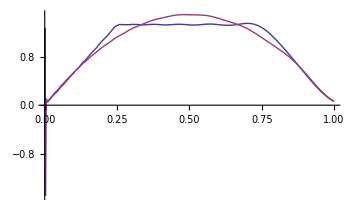

```mathematica
ListPlot[{dist,distTest},Joined->True,PlotStyle->{Thick}, PlotRange->{{0.0,1.0},{-1.5,1.5}} ]
```

```mathematica
(* The above plot shows that replacement of continuous wt fn rho[zz] by discrete zz pts = 1/2 and -1/2 puts sharp corners at x = 0 + 1/4 and x= 1-1/4.  In general use of 4 discrete zz pts will cause 4 sharp corners in the resulting distribution.   The continuous rho[zz] is needed to give a smooth result for dist(x) *)
```

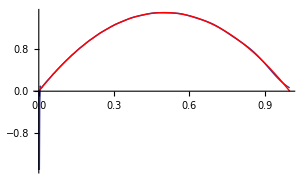

```mathematica
(* Just to make sure nothing went wrong compare exact reconstructed result to 6x(1-x) *)
Show[ListPlot[distTest,Joined->True, PlotRange->{{0.0,1.0},{-1.5,1.5}}],Plot[6x(1-x),{x,0,1},PlotStyle->Red]]
```

```mathematica
(* PCT:  Check integer moments of flat-top distn: [0,a/2]->linear up, [a/2,1-a/2]-> h=const, [1-a/2,1]-> linear down h is fixed in terms of a by norm  Does this come from sampling only at zz = -a, +a  ?    *)
```

```mathematica
a=1/2;h=2/(2-a);
```

```mathematica
f1[x_]:=2h x/a;f2[x_]:=h;f3[x_]:=2h (1-x)/a;
```

```mathematica
flatmomm=Simplify[ Integrate[x^mm f1[x],{x,0,a/2}] + Integrate[x^mm f2[x],{x,a/2,1-a/2}]+ Integrate[x^mm f3[x],{x,1-a/2,1}] ]
```

ConditionalExpression[(4^-mm (-1-3^(2+mm)+4^(2+mm)))/(3 (1+mm) (2+mm)),Re[mm]>-2]

```mathematica
(* This agrees with results from limitation to zz= -1/2, =1/2  *)
```